# Turmite

### Author

Eric W. Weisstein
January 27, 2011

This notebook downloaded from http://mathworld.wolfram.com/notebooks/ComputationalSystems/Turmite.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Turmite.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

Much of this material was inspired by A New Kind of Science.  See pages 930&931.

Many of these figures were originally discovered by Christopher Langton, James Propp, Rudy Rucker, Allen Brady, and Ken Krugler.

### Initialization

```mathematica
<<MathWorld`CellularAutomata`
```

## Code

By Ed Pegg Jr.

Note the arbitrary size limitation for the generated matrices.

```mathematica
mound = {{{0}},{1,1},{0,0}};
```

```mathematica
PadCenter[A_List,max_List] := PadRight[PadLeft[A,Floor[(Dimensions[A]+max)/2]],max]
```

A Turmite is a rule for a moving cell on a grid. Also called a 2D Turing Machine.
mite: moving cell with {state, direction}.
mound:  {matrix of colored cells, the position of the mite, {state,direction} of mite}.
state: matrix row in the turmite rule that will be used next. A two-state has values {0,1}.
color: matrix column used in the rule, color for grid cell to changed to. Two color has values {0=Black, 1=White}.
twist: change in direction for mite {Left=-1, No change=0, Right = 1}.
direction: current orientation of mite {0=^ ,1=> ,2=v, 3=<}
turmite: A rule that moves in the indicated direction, considers the current {color, state}, and changes the {color, direction, state} accordingly.
{{w0→ BN1,  b0→ BR0}, {w1→ BR1, b1→ WN0}}
{{{1,0,1},{1,-1,0}},{{1,1,1},{0,0,0}}}

PixelPerfect renders grid-based images without distortion.

```mathematica
moundstep[mound_List,turmite_List] := With[{
j=Dimensions[mound[[1]]][[1]],
k=Dimensions[mound[[1]]][[2]],
x=mound[[2,1]],
y=mound[[2,2]],
state=mound[[3,1]]+1,
direction = mound[[3,2]]},
If[Max[j,k]<129,  (* *** Arbitrarily maximum size of diagram *** *)
With[{old=Switch[direction,
0,If[x==1,{Prepend[mound[[1]],Table[0,{k}]],{x,y}},{mound[[1]],{x-1,y}}],
1,If[y==1 ,{Map[Prepend[#,0]&,mound[[1]]],{x,y}},{mound[[1]],{x,y-1}}],
2,If[x==j,{Append[mound[[1]],Table[0,{k}]],{x+1,y}},{mound[[1]],{x+1,y}}],3,If[y==k,{Map[Append[#,0]&,mound[[1]]],{x,y+1}},{mound[[1]],{x,y+1}}]]},
With[{newx = old[[2,1]],newy=old[[2,2]]},
With[{color=old[[1,newx,newy]]+1},
Append[ReplacePart[old,turmite[[state,color,1]],{1,newx,newy}],{turmite[[state,color,3]],Mod[direction + turmite[[state,color,2]],4]}]]]],{mound[[1]]}]];
```

```mathematica
myturmites={{{{1,1,0},{0,-1,0}}},
{{{0,-1,1},{1,1,1}},{{1,0,0},{1,0,1}}},{{{0,0,1},{0,-1,1}},{{1,1,0},{0,0,1}}},{{{0,1,1},{0,-1,0}},{{1,-1,1},{0,1,0}}},{{{0,1,1},{0,-1,0}},{{1,-1,1},{1,0,0}}},

{{{0,1,1},{0,0,1}},{{1,1,1},{1,-1,0}}},{{{0,1,1},{0,1,1}},{{1,0,0},{0,1,1}}},{{{0,1,1},{1,1,1}},{{1,-1,1},{1,-1,0}}},{{{1,-1,0},{0,0,1}},{{0,-1,0},{0,-1,1}}},{{{1,-1,0},{1,1,1}},{{0,1,0},{0,-1,1}}},

{{{1,-1,0},{1,1,1}},{{0,1,1},{1,-1,0}}},{{{1,-1,1},{0,-1,0}},{{1,0,0},{0,0,0}}},{{{1,-1,1},{0,-1,0}},{{1,1,1},{1,1,0}}},{{{1,-1,1},{0,-1,1}},{{1,1,1},{0,-1,0}}},{{{1,-1,1},{0,0,0}},{{1,0,0},{1,1,0}}},

{{{1,-1,1},{0,1,0}},{{0,-1,0},{0,-1,0}}},{{{1,-1,1},{1,-1,1}},{{1,1,1},{0,0,0}}},{{{1,-1,1},{1,1,0}},{{0,-1,0},{0,-1,0}}},{{{1,-1,1},{1,1,1}},{{1,0,0},{0,0,1}}},{{{1,0,1},{0,-1,1}},{{1,1,0},{1,0,1}}},

{{{1,0,1},{0,0,0}},{{0,1,0},{1,-1,0}}},{{{1,0,1},{0,0,1}},{{1,1,1},{0,0,0}}},{{{1,0,1},{0,1,0}},{{0,-1,0},{0,-1,0}}},{{{1,0,1},{0,1,1}},{{1,-1,0},{1,1,0}}},{{{1,0,1},{1,-1,0}},{{1,1,1},{0,0,0}}},

{{{1,1,0},{0,-1,1}},{{1,-1,0},{0,0,1}}},{{{1,1,0},{0,-1,1}},{{1,-1,0},{0,1,1}}},{{{1,1,0},{1,1,1}},{{0,0,0},{0,0,1}}},{{{1,1,1},{0,-1,1}},{{1,0,0},{0,0,0}}},{{{1,1,1},{0,1,0}},{{0,-1,1},{1,-1,0}}},

{{{1,1,1},{0,1,0}},{{0,0,0},{1,1,1}}},{{{1,1,1},{0,1,1}},{{1,0,0},{1,0,1}}},{{{1,1,1},{1,-1,1}},{{1,1,1},{0,1,0}}},{{{1,1,1},{1,0,0}},{{1,0,0},{0,0,1}}},{{{1,1,1},{1,1,0}},{{0,0,0},{0,0,0}}},

{{{1,1,1},{1,1,0}},{{0,1,0},{1,0,1}}},{{{1,1,1},{1,1,1}},{{1,-1,1},{0,1,0}}},{{{0,1,1},{1,1,1}},{{0,-1,2},{0,-1,0}},{{1,1,2},{1,-1,0}}},{{{1,-1,1},{0,0,0}},{{0,1,2},{1,-1,0}},{{1,1,1},{1,0,0}}},{{{1,-1,1},{0,0,2}},{{0,1,2},{1,0,1}},{{1,1,1},{1,0,0}}},

{{{1,-1,1},{1,-1,1}},{{1,0,0},{0,0,2}},{{0,-1,1},{1,0,1}}},{{{1,-1,2},{0,1,0}},{{1,-1,0},{0,1,0}},{{0,-1,0},{0,-1,1}}},{{{1,1,0},{0,1,2}},{{0,-1,0},{0,1,0}},{{0,0,1},{1,-1,0}}},{{{1,1,1},{0,-1,0}},{{1,1,2},{0,0,0}},{{1,-1,0},{0,-1,0}}}};
```

```mathematica
mybusybeaver ={{{0,1,1},{1,1,0}},{{1,1,0},{0,-1,1}}};
```

## Graphics

```mathematica
Pad[m0_List,n_]:=Module[{m,h=Floor[(n-Length[m0])/2]},
m=If[Length[m0[[1]]]==1,PadRight[#,2]&/@m0,m0];
Join[Table[0,{h},{2}],m,Table[0,{n-h-Length[m0]},{2}]]
]
```

```mathematica
First/@NestWhileList[moundstep[#,myturmites[[1]]]&,mound,Length[#]>1 &,1,10]
```

{{{0}},{{1},{0}},{{1,1},{0,0}},{{1,1},{1,0}},{{1,1},{1,1}},{{1,0},{1,1}},{{1,0,1},{1,1,0}},{{0,0,1},{1,0,1},{1,1,0}},{{0,1,1},{1,0,1},{1,1,0}},{{0,1,1},{1,1,1},{1,1,0}},{{0,1,1},{1,1,0},{1,1,0}}}

```mathematica
mound
```

{{{0}},{1,1},{0,0}}

```mathematica
PixelPerfect[NestWhile[moundstep[#,myturmites[[1]]]&,mound,Length[#]>1 &,1,1000000][[1]]]//Timing
```

{9.15 Second,Null}

## Binary

The rule shown below mimics binary counting.

#### V5

```mathematica
Show[Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{1.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,1}],Rectangle[{1.3,1.1},{1.7,1.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"1",{.5,.5},{0,-1}},
{"1",{1.5,.5},{1,0}},{"1",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,1},{2,1},{2,0},{0,0}}],Line[{{1.3,1.1},{1.3,1.5},{1.7,1.5},{1.7,1.1},{1.3,1.1}}],
Line[{{.3,1.1},{.3,1.5},{.7,1.5},{.7,1.1},{.3,1.1}}],
Line[{{1,0},{1,1}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False]
]
```

⁃Graphics⁃

```mathematica
binary={{{1,1,0},{0,0,0}}};
```

```mathematica
MatrixForm/@(l2=First/@NestWhileList[moundstep[#,binary]&,{Table[0,{4},{2}],{3,2},{0,0}},Length[#]>1 &,1,10])
```

{(0 | 0
0 | 0
0 | 0
0 | 0),(0 | 0
0 | 1
0 | 0
0 | 0),(0 | 0
1 | 1
0 | 0
0 | 0),(0 | 0
1 | 1
1 | 0
0 | 0),(0 | 0
1 | 1
1 | 1
0 | 0),(0 | 0
1 | 0
1 | 1
0 | 0),(0 | 1
1 | 0
1 | 1
0 | 0),(1 | 1
1 | 0
1 | 1
0 | 0),(1 | 1
0 | 0
1 | 1
0 | 0),(1 | 1
0 | 0
0 | 1
0 | 0),(1 | 1
0 | 0
0 | 1
1 | 0)}

```mathematica
d=With[{n=500},
l=First/@NestWhileList[moundstep[#,binary]&,mound,Length[#]>1 &,1,n];(f1=Function[f,FromDigits[First/@Take[f,Ceiling[Length[f]/2]],2]][#1];
f2=Function[f,FromDigits[Last/@Take[f,Ceiling[Length[f]/2]],2]][#1];
If[f1==f2,c=f1];
c)&/@l
]
```

{0,1,1,1,1,1,1,1,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,10,10,10,10,10,10,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,21,21,21,21,21,21,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,34,34,34,34,34,34,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,45,45,45,45,45,45,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,50,50,50,50,50,50,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,53,53,53,53,53,53,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,58,58,58,58,58,58,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,61,61,61,61,61,61,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64}

```mathematica
Length/@Split[d]
```

{1,7,6,8,8,6,6,10,10,6,6,8,8,6,6,12,12,6,6,8,8,6,6,10,10,6,6,8,8,6,6,14,14,6,6,8,8,6,6,10,10,6,6,8,8,6,6,12,12,6,6,8,8,6,6,10,10,6,6,8,8,6,6,16,7}

```mathematica
movie=Show/@With[{n=40},
c=0;
l=First/@NestWhileList[moundstep[#,binary]&,{Table[0,{6},{2}],{4,2},{0,0}},Length[#]>1 &,1,n];
d=Length[Last[l]];
MapIndexed[Graphics[
{
Graphics[DensityGraphics[1-Reverse[#1],Frame->False,AspectRatio->Automatic]][[1]],
Table[{
Text[i,{2.5,+i-.5+Floor[d/2]}],
Text[-i,{2.5,-i+.5+Floor[d/2]}]
},{i,d/2}],
{RGBColor[1,0,0],Thickness[.02],Line[{{0,#},{2,#}}&[Floor[d/2]]]}
},
AspectRatio->Automatic,
PlotLabel->(f1=Function[f,FromDigits[First/@Take[f,Ceiling[Length[f]/2]],2]][#1];
f2=Function[f,FromDigits[Last/@Take[f,Ceiling[Length[f]/2]],2]][#1];
If[f1==f2,c=f1];
If[#2[[1]]<2,c=0];
TraditionalForm["it: "<>ToString[#2[[1]]]<>", binary: "<>ToString[c]]
)
]&,Rest[l]
]
]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
Show[GraphicsArray[Partition[Take[movie,12],6]]]
```

⁃GraphicsArray⁃

```mathematica
<<Utilities`GIF`
```

{ByteOrdering:>$ByteOrdering,CharacterEncoding→Automatic,ConversionOptions→{Loop→True,AnimationDisplayTime→0.1},ImageResolution→Automatic,ImageRotated→False,ImageSize→Automatic}

```mathematica
Export[gifs<>"turmbin.gif",movie]//Timing
```

{10.09 Second,/Volumes/Data/Troves/MathOzTeX/newgifs/turmbin.gif}

#### V6

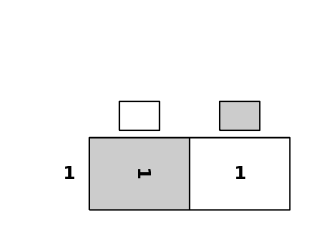

```mathematica
Show[Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{1.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,1}],Rectangle[{1.3,1.1},{1.7,1.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"1",{.5,.5},{0,-1}},
{"1",{1.5,.5},{1,0}},{"1",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,1},{2,1},{2,0},{0,0}}],Line[{{1.3,1.1},{1.3,1.5},{1.7,1.5},{1.7,1.1},{1.3,1.1}}],
Line[{{.3,1.1},{.3,1.5},{.7,1.5},{.7,1.1},{.3,1.1}}],
Line[{{1,0},{1,1}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False]
]
```

```mathematica
binary={{{1,1,0},{0,0,0}}};
```

```mathematica
MatrixForm/@(l2=First/@NestWhileList[moundstep[#,binary]&,{Table[0,{4},{2}],{3,2},{0,0}},Length[#]>1 &,1,10])
```

{(0 | 0
0 | 0
0 | 0
0 | 0),(0 | 0
0 | 1
0 | 0
0 | 0),(0 | 0
1 | 1
0 | 0
0 | 0),(0 | 0
1 | 1
1 | 0
0 | 0),(0 | 0
1 | 1
1 | 1
0 | 0),(0 | 0
1 | 0
1 | 1
0 | 0),(0 | 1
1 | 0
1 | 1
0 | 0),(1 | 1
1 | 0
1 | 1
0 | 0),(1 | 1
0 | 0
1 | 1
0 | 0),(1 | 1
0 | 0
0 | 1
0 | 0),(1 | 1
0 | 0
0 | 1
1 | 0)}

```mathematica
d=With[{n=500},
l=First/@NestWhileList[moundstep[#,binary]&,mound,Length[#]>1 &,1,n];(f1=Function[f,FromDigits[First/@Take[f,Ceiling[Length[f]/2]],2]][#1];
f2=Function[f,FromDigits[Last/@Take[f,Ceiling[Length[f]/2]],2]][#1];
If[f1==f2,c=f1];
c)&/@l
]
```

{0,1,1,1,1,1,1,1,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,10,10,10,10,10,10,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,21,21,21,21,21,21,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,34,34,34,34,34,34,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,45,45,45,45,45,45,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,50,50,50,50,50,50,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,53,53,53,53,53,53,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,58,58,58,58,58,58,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,61,61,61,61,61,61,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64}

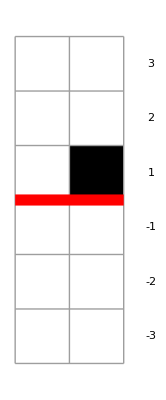
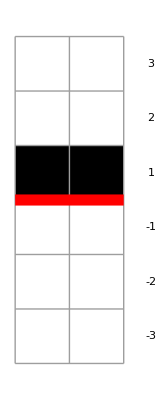
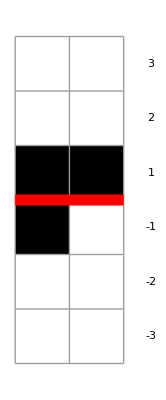
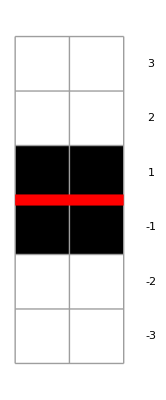
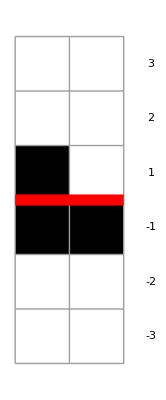
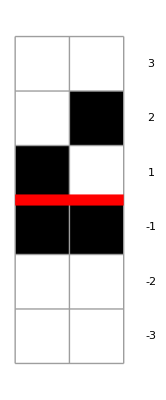
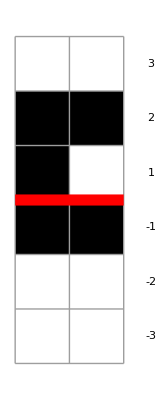
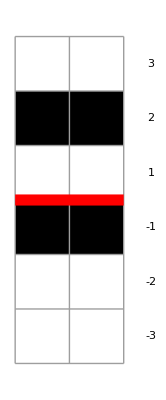

```mathematica
movie=Show/@With[{n=40},
c=0;
l=First/@NestWhileList[moundstep[#,binary]&,{Table[0,{6},{2}],{4,2},{0,0}},Length[#]>1 &,1,n];
d=Length[Last[l]];
MapIndexed[Graphics[
{
Graphics[ArrayPlot[Reverse[#1],DataReversed->True,Mesh->True,Frame->False,AspectRatio->Automatic]][[1]],
Table[{
Text[i,{2.5,+i-.5+Floor[d/2]}],
Text[-i,{2.5,-i+.5+Floor[d/2]}]
},{i,d/2}],
{RGBColor[1,0,0],Thickness[.02],Line[{{0,#},{2,#}}&[Floor[d/2]]]}
},
AspectRatio->Automatic
(*
PlotLabel->(f1=Function[f,FromDigits[First/@Take[f,Ceiling[Length[f]/2]],2]][#1];
f2=Function[f,FromDigits[Last/@Take[f,Ceiling[Length[f]/2]],2]][#1];
If[f1==f2,c=f1];
If[#2[[1]]<2,c=0];
TextCell["it: "<>ToString[#2[[1]]]<>", binary: "<>ToString[c]]
)
*)
]&,Rest[l]
]
]
```

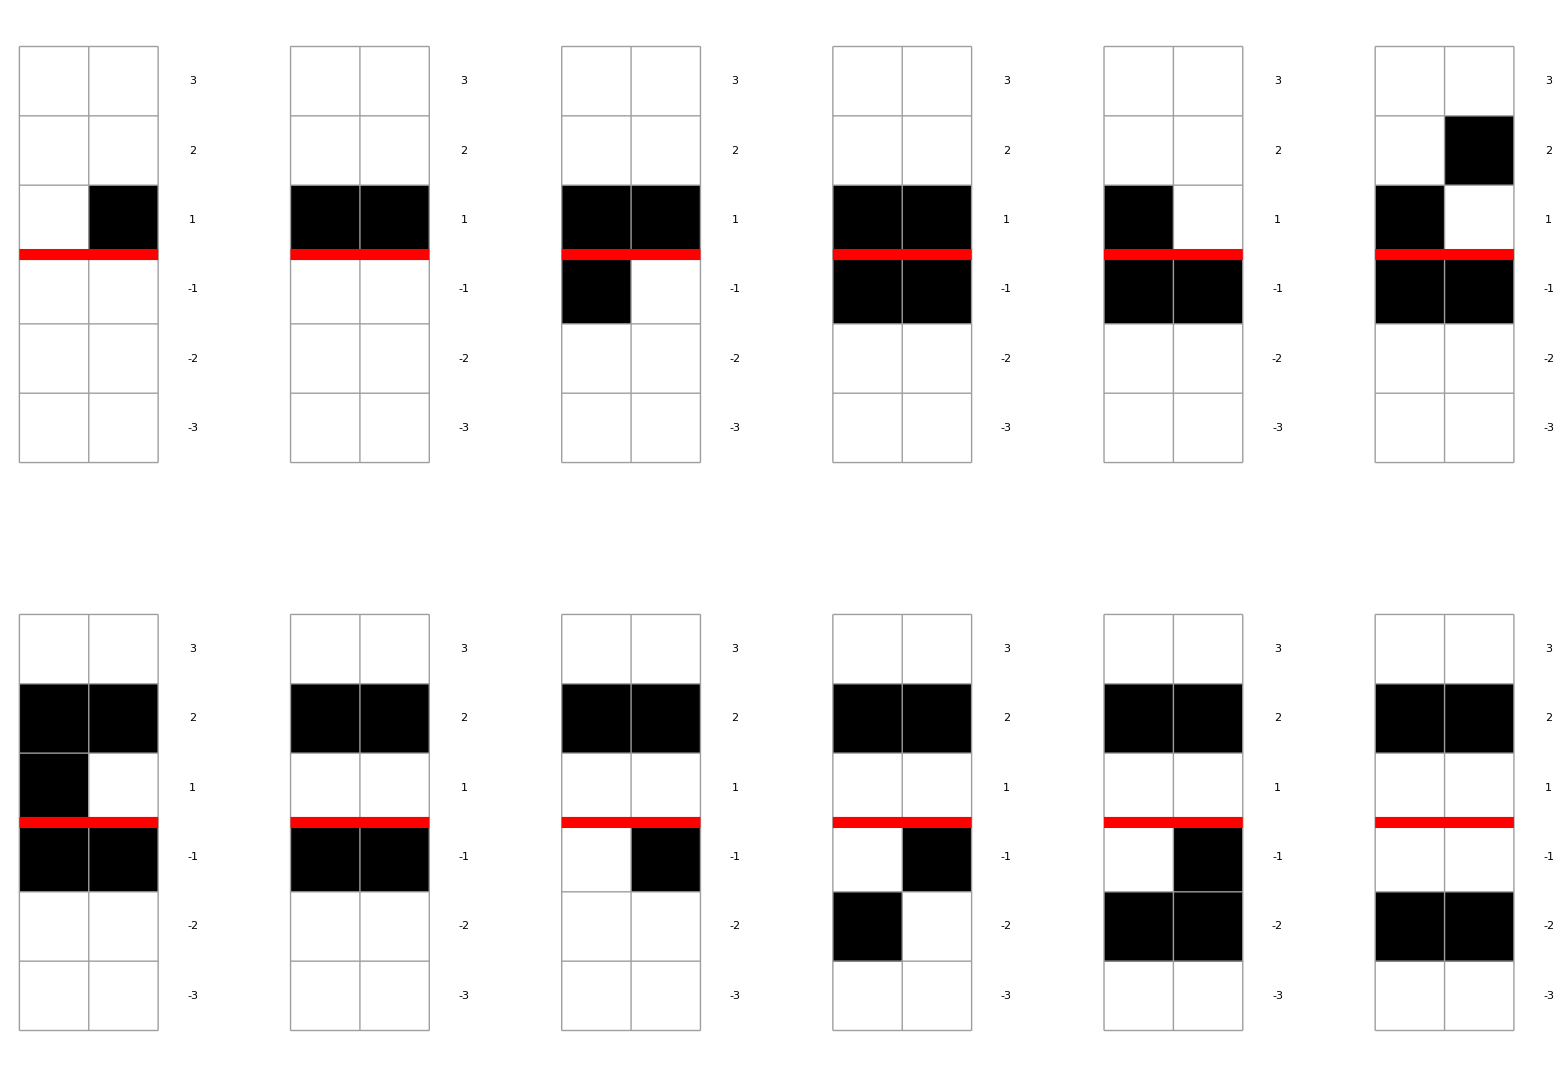

```mathematica
GraphicsGrid[Partition[Take[movie,12],6],Spacings->100]
```

### Change color of underlying cell If on black, turn right. If on white, continue straight.

By Ed Pegg Jr.

This rule produces binary, as seen below.

```mathematica
A=Table[0,{2},{30}];
Compass={{0,1},{-1,0},{0,-1},{1,0}};
CurrentDirection=1;
{x,y}={2,16};
g={};

Do[
A[[x,y]]=-BitNot[-A[[x,y]]];
If[{x,y}=={2,15},AppendTo[g,Graphics[Raster[Mod[A-1,2]],AspectRatio->Automatic]]
];
If[A[[x,y]]==1,CurrentDirection=Mod[CurrentDirection,4]+1];
{x,y}={x,y}+Compass[[CurrentDirection]],
{n,1,125}];
```

```mathematica
Show/@g
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
A=Table[0,{2},{30}];
Compass={{0,1},{-1,0},{0,-1},{1,0}};
CurrentDirection=1;
{x,y}={2,16};
B = {};

Do[
A[[x,y]]=-BitNot[-A[[x,y]]];
If[{x,y}=={2,15},B=Append[B,n]];
If[A[[x,y]]==1,CurrentDirection=Mod[CurrentDirection,4]+1];
{x,y}={x,y}+Compass[[CurrentDirection]];
,{n,1,313}]
```

The behavior for when the turing machine counts is well-behaved.

```mathematica
B/4
```

{1,3,4,7,8,10,11,15,16,18,19,22,23,25,26,31,32,34,35,38,39,41,42,46,47,49,50,53,54,56,57,63,64,66,67,70,71,73,74,78}

```mathematica
Table[FactorInteger[(2 n)!][[1,2]],{n,1,40}]
```

{1,3,4,7,8,10,11,15,16,18,19,22,23,25,26,31,32,34,35,38,39,41,42,46,47,49,50,53,54,56,57,63,64,66,67,70,71,73,74,78}

```mathematica
Table[2 n - Apply[Plus,IntegerDigits[2 n,2]],{n,1,40}]
```

{1,3,4,7,8,10,11,15,16,18,19,22,23,25,26,31,32,34,35,38,39,41,42,46,47,49,50,53,54,56,57,63,64,66,67,70,71,73,74,78}

```mathematica
(Drop[B,1]-Drop[B,-1])/4
```

{2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3,1,2,1,4}

```mathematica
ListPlot[%];
```

```mathematica
Export[gifs<>"turmbin.gif",movie]//Timing
```

{9.63 Second,/Volumes/Data/Troves/MathOzTeX/newgifs/turmbin.gif}

## Highways

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{1,29,14,32}],1]]]
```

The second image above, a 2-state 2-color rule, is essentially Langton's ant again.  Pictorial representations of all four rules are given in the look-up tables below. In the second rule, for example, if the state is 1, and the underlying cell is gray, then change the cell to white, change the state to 2, and turn left.

### Turmite Rule Graphic Code

```mathematica
turmiterulegraphic =GraphicsArray[{Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{1.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,1}],Rectangle[{1.3,1.1},{1.7,1.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"1",{.5,.5},{0,-1}},
{"1",{1.5,.5},{0,1}},{"1",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,1},{2,1},{2,0},{0,0}}],Line[{{1.3,1.1},{1.3,1.5},{1.7,1.5},{1.7,1.1},{1.3,1.1}}],
Line[{{.3,1.1},{.3,1.5},{.7,1.5},{.7,1.1},{.3,1.1}}],
Line[{{1,0},{1,1}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False],Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{2.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,2}],Rectangle[{1.3,2.1},{1.7,2.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"2",{.5,1.5},{0,-1}},{"2",{1.5,1.5},{0,1}},{"1",{.5,.5},{1,0}},
{"1",{1.5,.5},{1,0}},{"1",{-.2,1.5},{1,0}},{"2",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,2},{2,2},{2,0},{0,0}}],Line[{{1.3,2.1},{1.3,2.5},{1.7,2.5},{1.7,2.1},{1.3,2.1}}],
Line[{{.3,2.1},{.3,2.5},{.7,2.5},{.7,2.1},{.3,2.1}}],
Line[{{1,0},{1,2}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False],Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{2.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,2}],Rectangle[{1.3,2.1},{1.7,2.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"2",{.5,1.5},{0,1}},{"2",{1.5,1.5},{0,1}},{"2",{.5,.5},{0,-1}},
{"1",{1.5,.5},{0,1}},{"1",{-.2,1.5},{1,0}},{"2",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,2},{2,2},{2,0},{0,0}}],Line[{{1.3,2.1},{1.3,2.5},{1.7,2.5},{1.7,2.1},{1.3,2.1}}],
Line[{{.3,2.1},{.3,2.5},{.7,2.5},{.7,2.1},{.3,2.1}}],
Line[{{1,0},{1,2}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False],Graphics[{GrayLevel[1],
Rectangle[{-.6,-.1},{2.1,2.6}],GrayLevel[.8],Rectangle[{0,0},{1,2}],Rectangle[{1,0},{2,1}],Rectangle[{1.3,2.1},{1.7,2.5}],
GrayLevel[0],Map[Text[StyleForm[#[[1]],FontSize->18,FontFamily-> "Courier",FontWeight->"Bold"],#[[2]],{0,0},#[[3]]] &,{{"2",{.5,1.5},{0,-1}},{"2",{1.5,1.5},{0,-1}},{"1",{.5,.5},{1,0}},
{"2",{1.5,.5},{1,0}},{"1",{-.2,1.5},{1,0}},{"2",{-.2,.5},{1,0}}}],
Line[{{0,0},{0,2},{2,2},{2,0},{0,0}}],Line[{{1.3,2.1},{1.3,2.5},{1.7,2.5},{1.7,2.1},{1.3,2.1}}],
Line[{{.3,2.1},{.3,2.5},{.7,2.5},{.7,2.1},{.3,2.1}}],
Line[{{1,0},{1,2}}],Line[{{0,1},{2,1}}]},AspectRatio-> Automatic,Frame-> False]}];
```

### Turmite Rule Graphic

```mathematica
Show[turmiterulegraphic]
```

⁃GraphicsArray⁃

Above, the structures called ``highways'' all travel down and to the right. Other possible highways are illustrated below.  In the third image, the highway gets thicker as it lengthens.

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{12,43,11,44}],1]]]
```

Growth around the edges is frequently seen. The fourth image illustrates a turmite which will grow even within a field of sparse random data.

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{24,15,7,25}],1]]]
```

\hrefacc{Spirals}{Spiral} are quite common. The second turmite below constructs a \href{golden rectangle}.

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{3,17,4,19}],1]]]
```

Chaotic behavior of many different types can happen.  For the first turmite below, a million steps are shown.  The fourth displays more counting behavior.

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{18,10,9,16}],1]]]
```

```mathematica
PixelPerfect[Transpose[Flatten[Map[Function[x,Transpose[
PadCenter[NestWhile[moundstep[#,myturmites[[x]]]&,mound,Length[#]>1 &,1,1000000][[1]],{131,131}]]],{33,6,38,21}],1]]]
```

In addition to persistent structures, nested growth, and chaotic behavior, it is possible for the turmite to cycle in a loop of arbitrary size.  Whether or not this ever happens is an NP-complexity problem, much like the \href{busy beaver} problem. Below is a sample turmite that gets trapped in a cycle after some amount of growth.

```mathematica
PixelPerfect[NestWhile[moundstep[#,mybusybeaver]&,mound,Length[#]>1 &,1,100000][[1]]]
```